```mathematica
f={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),Nt1+Nt2==N};
f//TableForm
```

(1-τ)/(Nt1-A1 τ)==(1-τ)/(Nt2-A2 τ)
Nt1+Nt2==N

```mathematica
res=Solve[f,{Nt1,Nt2}]
```

{{Nt1→N/2+(A1 τ)/2-(A2 τ)/2,Nt2→N/2-(A1 τ)/2+(A2 τ)/2}}

```mathematica
manu[A1_,A2_,τ_]:=Evaluate[res[[1,{1,2},2]]/.N->2]
```

```mathematica
Manipulate[Plot[Evaluate[manu[A1,A2,τ]],{τ,0,1},PlotRange->2],{{A1,0.5},0,1},{A2,0,1}]
```

模拟mono标准测试的结果

```mathematica
Manipulate[ListPlot[
(Table[manu[t,a2,0.75],{t,0,1,0.02}]~Join~Table[manu[t,a2,0.75],{t,1,0,-0.02}])ᵀ~Join~{Range[0,1,0.02]~Join~Range[1,0,-0.02]},
PlotLabel->"mono",PlotStyle->PointSize[Tiny],PlotRange->{0,1.5}
],{{a2,0.5},0,1}]
```

模拟random测试集的结果

```mathematica
r=RandomReal[1,50];
Manipulate[ListPlot[manu[#,a2,0.75]&/@rᵀ~Join~{r},Filling->Axis,PlotRange->1.5],{{a2,0.5},0,1}]
```

```mathematica
t={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt3-τ A3),Nt1+Nt2+Nt3==n};
```

```mathematica
t=Solve[t,{Nt1,Nt2,Nt3}];
```

```mathematica
manu3[A1_,A2_,A3_,τ_]:=Evaluate[t[[1,All,2]]/.n->3]
```

```mathematica
Manipulate[Plot[Evaluate[manu3[A1,A2,A3,τ]],{τ,0,1},PlotRange->3],{{A1,0.75},0,1},{{A2,0.5},0,1},{A3,0,1}]
```

```mathematica
Manipulate[Plot[Evaluate[manu[A1,A2,τ]-{A1,A2}],{τ,0,1},PlotRange->2],{{A1,0.5},0,1},{A2,0,1}]
```

```mathematica
manu[A1,A2,τ]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

为了研究τ的范围.现在我们来观察下面一个事实.
1.在总内存能够满足分配的时候.需要分配的量大于等于申请的量也就是N_ti>=A_i.
   否则.会得出明明还有富余但是给你分配的反而无法满足需求的不可理解的情况.
所以列出方程{Nt1>=A1,Nt2>=A2,A1+A2<=N}最后根据τ画出来解区域.

```mathematica
Manipulate[RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2,{A1,0,2},{A2,0,2}],{{τ,0.75},0,2}]
```

为了分析.我们取出一些片段来分析.

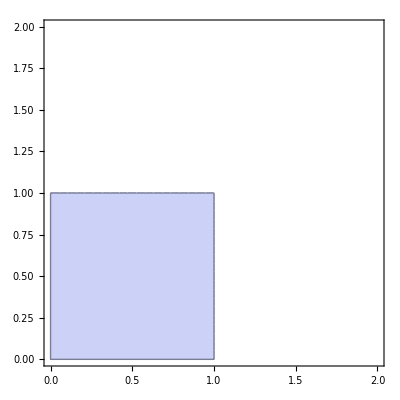

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->0,{A1,0,2},{A2,0,2}]
```

这个是τ等于0的时候的结果.可以看到.其中满足解的范围非常小.要求A1,A2<=1.也就是小于等于各自的初始内存.不能超过它.不然解就会违反条件1.
这个是非常的不合理的.
下面再看一下τ=0.75的情况

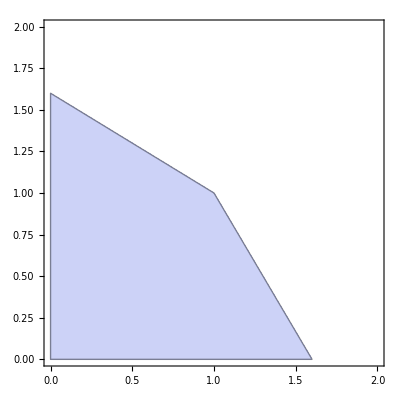

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->0.75,{A1,0,2},{A2,0,2}]
```

由此图可以看出.解区域的面积已经大于了τ=0的情况了.但是.明显的.还有一些问题.例如.1.5,0.5这个组合就无法满足解.也就是说.在τ=0.75的时候不能够提出一台虚拟机申请的内存是另外一台的3倍.
否则解就会异常.准确的来说.解出来的结果是manu[1.5,0.5,0.75]={1.375, 0.625},申请1.5却只能得到1.35.
下面再来看τ=1的情况.

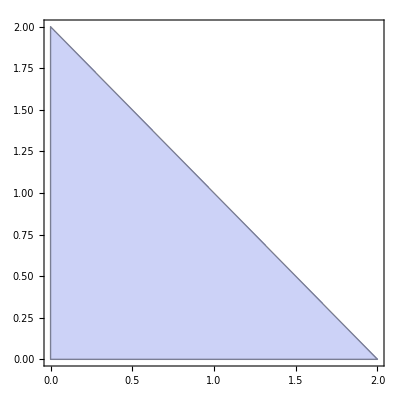

```mathematica
RegionPlot[1+(A1 τ)/2-(A2 τ)/2≥A1&&1-(A1 τ)/2+(A2 τ)/2≥A2&&A1+A2≤2/.τ->1,{A1,0,2},{A2,0,2}]
```

这个时候.解面积最大.在所有可以满足的情况下.都能够得到合理的解.
所以τ应该为1.

造成这种现象的原因是.整个解可以看作是N/n+Δ(A_i).所以第1项的N/n决定了解的性质.上下偏离的常数范围.

求反驳.